#### Mathematica file to compute New Physics contributions to g-2. Acknowledgments should be referred to: Farinaldo S. Queiroz and William Shepherd [arxiv:1403.2309] and M Lindner, M Platscher, FS Queiroz, e-Print: 1610.06587v2, [hep-ph]• DOI: 10.1016/j.physrep.2017.12.001 A. S. de Jesus, S. Kovalenko, C. A. de S. Pires, F. S. Queiroz, and Y. S. Villamizar Phys. Lett. B, vol. 809, p. 135689, 2020. e-Print: 2003.06440 [hep-ph]•DOI: 10.1016/j.physletb.2020.135689 (publication) M. Lindner, M. Platscher, and F. S. Queiroz Phys. Rept. vol. 731, pp. 1-82, 2018. e-Print: 1610.06587 • DOI: 10.1016/j.physrep.2017.12.001 Yoxara S. Villamizar, Farinaldo S. Queiroz, Alvaro S. de Jesus, Sergey Kovalenko, and C. A. de S. Pires. Implications of the Muon Anomalous Magnetic Moment for 3-3-1 Models. PoS EPS-HEP2021 (2022) 638 • DOI: 10.22323/1.398.0638 (publication)

The reader should straightforwardly use this mathematica file to compute the total contribution of a generic model to the muon magnetic moment at 1-loop level. Plots are also available. We have closely followed the notation of our paper arxiv:

New Physics Contribution to (g-2)_μ

## 3-3-1 Exotic Leptons M_N = 100GeV, M_E = 500GeV

Global Parameters. 
Masses of the SM particles in GeV units.

```mathematica
mμ=0.105;(*Muon mass*)mν=0.1*10^-9;(*Neutrino mass*)Mw=80;(*W boson mass*)MZ=90;(*Z mass*)Mh=125;(*Higgs mass*)g=0.65;v=240;mN=100;mE=500;sw2=0.231 (*SW^2*);sw=Sqrt[sw2];cw=Sqrt[1-sw2];c2w=cw^2-sw^2;
cw2=1-sw2;tgw=sw/cw;
gp=(g*tgw)/Sqrt[(1-(tgw^2/3))];
gv=(-c2w+(2*sw^2))/2;
ga=(c2w+(2*sw^2))/2;
θ=0.001(*W-V mixing angle*);
```

Experimental Bounds
based on:
Current Bound: (261 ± 78) x 10^-11;
Projected 1 sigma bound < 34 x 10^-11;

```mathematica
BoundCurrenteup=Table[{x,339*10^-11},{x,1,10000,1}];
BoundCurrentdown=Table[{x,183*10^-11},{x,1,10000,1}];
sigmaCurrent=Table[{x,78*10^-11},{x,1,10000,1}];
sigmaProjected=Table[{x,34*10^-11},{x,1,10000,1}];
```

## 1. Z’ boson. L ~ gv9 Z' μ̄ γ^μ μ + ga9 Z' μ̄ γ^μγ^5 μ

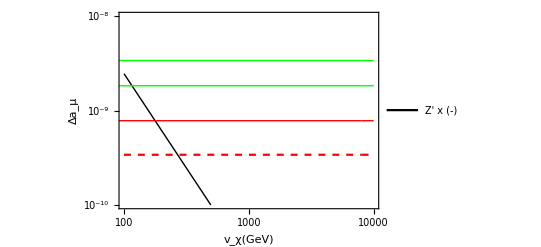

```mathematica
mf9=mμ; ϵ9=mf9/mμ;MZp=Sqrt[(2/9)*((3*g^2+gp^2))*Vqui^2];λ9=mμ/MZp;gv9=(gv*gp)/(2*Sqrt[3]*sw*cw);ga9=(ga*gp)/(2*Sqrt[3]*sw*cw);
ΔaZp=Table[{Vqui,(gv9^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2+2ϵ9)+λ9^2*(1-ϵ9)^2*x^2*(1+ϵ9-x))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] 
+ (ga9^2*mμ^2)/(8*π^2*MZp^2)*NIntegrate[(2*x*(1-x)*(x-2-2ϵ9)+λ9^2*(1+ϵ9)^2*x^2*(1-ϵ9-x))/((1-x)*(1-λ9^2*x)+ϵ9^2*λ9^2*x),{x,0,1}] },{Vqui,100,10000,500}];
size9=Dimensions[ΔaZp];
ΔaZpnew=Table[{ΔaZp[[i,1]],-ΔaZp[[i,2]]},{i,1,size9[[1]]}];
ListLogLogPlot[{ΔaZpnew,BoundCurrenteup,BoundCurrentdown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"Z' x (-)"}],{0.7,0.92}]]
```

```mathematica
(*Use the command below to save the figure. Ex:
Export["/home/Yoxara/Documents/331gmu/plot9.pdf",plot9];*)
```

## 2. Charged Vector Boson K+. L ~ gv10 k_μ^+ν̄ γ^μ μ + ga10 k_μ^+ν̄ γ^μγ^5 μ.

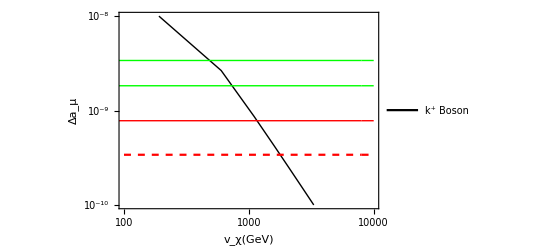

```mathematica
MKp=Sqrt[(g^4/4)*((2*Vqui^2)+v^2)];mf10=mN;ϵ10=mf10/mμ; λ10=mμ/MKp;gv10=g/(Sqrt[2]);ga10=g/(Sqrt[2]);
ΔaChargedVec=Table[{Vqui,-(gv10^2*mμ^2)/(8*π^2*MKp^2)*NIntegrate[(-2*x^2*(1+x-2*ϵ10)+λ10^2*(1-ϵ10)^2*x*(1-x)*(x+ϵ10))/(ϵ10^2*λ10^2*(1-x)*(1-ϵ10^-2*x)+x),{x,0,1}]+-(ga10^2*mμ^2)/(8*π^2*MKp^2)*NIntegrate[(-2*x^2*(1+x+2*ϵ10)+λ10^2*(1+ϵ10)^2*x*(1-x)*(x-ϵ10))/(ϵ10^2*λ10^2*(1-x)*(1-ϵ10^-2*x)+x),{x,0,1}]},{Vqui,100,10000,500}];
size10=Dimensions[ΔaChargedVec];
ΔaChargedVecnew=Table[{ΔaChargedVec[[i,1]],ΔaChargedVec[[i,2]]},{i,1,size10[[1]]}];
plot10=ListLogLogPlot[{ΔaChargedVecnew,BoundCurrenteup,BoundCurrentdown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"k⁺ Boson"}],{0.7,0.92}]]
```

3. Neutral vector boson k0

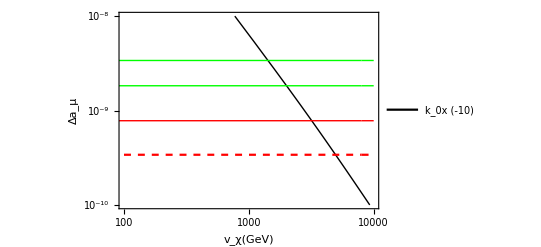

```mathematica
MK0=Sqrt[(g^4/4)*((2*Vqui^2)+v^2)];mf11=mE;ϵ11=mf11/mμ; λ11=mμ/MKp;gv11=-g/Sqrt[2];ga11=g/Sqrt[2];
ΔaK0=Table[{Vqui,(gv11^2*mμ^2)/(8*π^2*MK0^2)*NIntegrate[(2*x*(1-x)*(x-2+2ϵ11)+λ11^2*(1-ϵ11)^2*x^2*(1+ϵ11-x))/((1-x)*(1-λ11^2*x)+ϵ11^2*λ11^2*x),{x,0,1}] 
+ (ga11^2*mμ^2)/(8*π^2*MK0^2)*NIntegrate[(2*x*(1-x)*(x-2-2ϵ11)+λ11^2*(1+ϵ11)^2*x^2*(1-ϵ11-x))/((1-x)*(1-λ11^2*x)+ϵ11^2*λ11^2*x),{x,0,1}] },{Vqui,100,10000,500}];
size11=Dimensions[ΔaK0];
ΔaK0new=Table[{ΔaK0[[i,1]],-ΔaK0[[i,2]]*10},{i,1,size11[[1]]}];
ListLogLogPlot[{ΔaK0new,BoundCurrenteup,BoundCurrentdown,sigmaCurrent,sigmaProjected},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed]},Joined->True,PlotRange->{{100,10000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->Placed[LineLegend[{"k_0x (-10)"}],{0.7,0.92}]]
```

```mathematica
plottotal1=ListLogLogPlot[{ΔaChargedVecnew,ΔaK0new,ΔaZpnew,BoundCurrenteup,sigmaCurrent,sigmaProjected,BoundCurrentdown},PlotStyle->{Directive[Black,Thick],Directive[Gray,Thick,Dashed],Directive[Orange,Thick,DotDashed],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick]},Joined->True,PlotRange->{{100,8000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"k⁺","k⁰x(-10)","Z' x (-)","Δa_μ Current","Δa_μ Projected"}],PlotLabel->Style["3-3-1 Exotic Leptons",16,Black,Bold]]
```

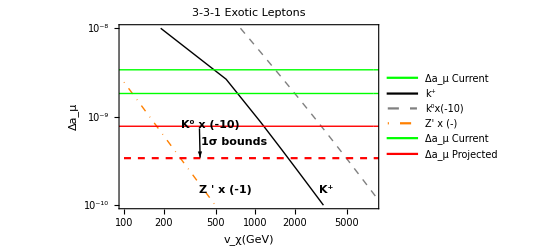

```mathematica
sizetotal=Dimensions[ΔaChargedVec]; 
sizetotal[[1]]
```

20

```mathematica
Totalcontri=Table[{ΔaChargedVec[[i,1]],ΔaChargedVec[[i,2]]+ΔaK0[[i,2]]+ΔaZp[[i,2]]},{i,1,sizetotal[[1]]}];
```

```mathematica
plottotal2=ListLogLogPlot[{Abs[Totalcontri],BoundCurrenteup,sigmaCurrent,sigmaProjected,BoundCurrentdown},PlotStyle->{Directive[Black,Thick],Directive[Green,Thick],Directive[Red,Thick],Directive[Red,Dashed],Directive[Green,Thick]},Joined->True,PlotRange->{{100,5000},{10^-10,10^-8}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[v,χ][GeV]],12,Black,Bold],Style[HoldForm[Subscript[Δa,μ]],15,Black,Bold]},PlotLegends->LineLegend[{"TotalContribution","Δa_μ Current","1σ Bound Current","1σ Bound Projected"}],PlotLabel->Style["3-3-1 Exotic Leptons",16,Black,Bold]]
```